```mathematica
(*Columbic interaction of charge*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}
```

Assumptions→{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}

```mathematica
rhoA[r_]:=A Exp[- α r]
rhoA[r]
```

A ⅇ^(-r α)

```mathematica
rhoB[r_]:=B Exp[-β r]
rhoB[r]
```

B ⅇ^(-r β)

```mathematica
phiA[r_]:=1/(ϵ)((1/r )Integrate[rhoA[x] x^2,{x,0,r}]+Integrate[x rhoA[x],{x,r,Infinity},Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

```mathematica
phiA[r]//Expand
```

(2 A)/(r α^3 ϵ)-(2 A ⅇ^(-r α))/(r α^3 ϵ)-(A ⅇ^(-r α))/(α^2 ϵ)

```mathematica
V1=(4 Pi A B/(α^3 *ϵ)(Integrate[r^2 Exp[-β r]*Integrate[1/Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 Exp[-β r]*Integrate[1/Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}]))//Simplify
```

(8 A B ⅇ^(-R β) π (-2+2 ⅇ^(R β)-R β))/(R α^3 β^3 ϵ)

```mathematica
V1E=V1/.{B->A,β->α}
```

(8 A^2 ⅇ^(-R α) π (-2+2 ⅇ^(R α)-R α))/(R α^6 ϵ)

```mathematica
V2=-4 Pi A B/(α^3*ϵ) (Integrate[r Exp[-α r]*Integrate[Exp[-β Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r Exp[-α r]*Integrate[Exp[-β Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-1/(α^3 ϵ)4 A B π (-(ⅇ^(-R (α+2 β)) (α-ⅇ^(2 R β) α+2 β-2 ⅇ^(2 R β) β+2 R α β+2 R β^2))/(R β^2 (α+β)^2)-(ⅇ^(-R (α+2 β)) (-α^3+ⅇ^(2 R β) α^3-2 R α^3 β+3 α β^2-3 ⅇ^(2 R β) α β^2+2 R α^2 β^2-2 ⅇ^(R (α+β)) R α^2 β^2-2 β^3-2 ⅇ^(2 R β) β^3+4 ⅇ^(R (α+β)) β^3+2 R α β^3-2 R β^4+2 ⅇ^(R (α+β)) R β^4))/(R β^2 (-α^2+β^2)^2))

```mathematica
V2//Simplify
```

-(8 A B ⅇ^(-R (α+2 β)) π (2 ⅇ^(2 R β) β+ⅇ^(R (α+β)) (-2 β+R (α^2-β^2))))/(R α^3 (α-β)^2 (α+β)^2 ϵ)

```mathematica
V2E=-4 Pi A ^2/(α^3*ϵ) (Integrate[r Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-1/(α^3 ϵ)4 A^2 π ((ⅇ^(-3 R α) (-3+3 ⅇ^(2 R α)-4 R α))/(4 R α^3)+(ⅇ^(-3 R α) (3-3 ⅇ^(2 R α)+4 R α+2 ⅇ^(2 R α) R α+2 ⅇ^(2 R α) R^2 α^2))/(4 R α^3))

```mathematica
V2E//Simplify
```

-(2 A^2 ⅇ^(-R α) π (1+R α))/(α^5 ϵ)

```mathematica
V3=-2Pi A B/(α^2 ϵ) (Integrate[r^2 Exp[-β r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 Exp[-β r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-1/(α^2 ϵ)2 A B π (-1/(R α^2 (α+β)^3)ⅇ^(-R (2 α+β)) (3 α-3 ⅇ^(2 R α) α+4 R α^2-2 ⅇ^(2 R α) R α^2+2 R^2 α^3+β-ⅇ^(2 R α) β+5 R α β-3 ⅇ^(2 R α) R α β+4 R^2 α^2 β+R β^2-ⅇ^(2 R α) R β^2+2 R^2 α β^2)+1/(R α^2 (α^2-β^2)^3)ⅇ^(-R (2 α+β)) (3 α^4-3 ⅇ^(2 R α) α^4+4 R α^5+2 ⅇ^(2 R α) R α^5+2 R^2 α^6-8 α^3 β-8 ⅇ^(2 R α) α^3 β+16 ⅇ^(R (α+β)) α^3 β-7 R α^4 β+3 ⅇ^(2 R α) R α^4 β+4 ⅇ^(R (α+β)) R α^4 β-2 R^2 α^5 β+6 α^2 β^2-6 ⅇ^(2 R α) α^2 β^2-2 R α^3 β^2-2 ⅇ^(2 R α) R α^3 β^2-4 R^2 α^4 β^2+8 R α^2 β^3-4 ⅇ^(2 R α) R α^2 β^3-4 ⅇ^(R (α+β)) R α^2 β^3+4 R^2 α^3 β^3-β^4+ⅇ^(2 R α) β^4-2 R α β^4+2 R^2 α^2 β^4-R β^5+ⅇ^(2 R α) R β^5-2 R^2 α β^5))

```mathematica
V3//Simplify
```

-((8 A B ⅇ^(-R (2 α+β)) π (ⅇ^(R (α+β)) β (4 α+R α^2-R β^2)+ⅇ^(2 R α) α (-4 β+R (α^2-β^2))))/(R α^2 (α-β)^3 (α+β)^3 ϵ))

```mathematica
V3E=-2Pi A ^2/(α^2*ϵ )(Integrate[r^2 Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,R},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]<Re[R]}]+Integrate[r^2 Exp[-α r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,R,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0,Re[r]>Re[R]}])
```

-1/(α^2 ϵ)2 A^2 π ((ⅇ^(-3 R α) (-2+2 ⅇ^(2 R α)-5 R α+3 ⅇ^(2 R α) R α-4 R^2 α^2))/(4 R α^4)+1/(12 R α^4)ⅇ^(-3 R α) (6-6 ⅇ^(2 R α)+15 R α-3 ⅇ^(2 R α) R α+12 R^2 α^2+6 ⅇ^(2 R α) R^2 α^2+2 ⅇ^(2 R α) R^3 α^3))

```mathematica
V3E//Simplify
```

-(A^2 ⅇ^(-R α) π (3+3 R α+R^2 α^2))/(3 α^5 ϵ)

```mathematica
(*Full potential two diff atoms*)
V=V1+V2+V3
```

(8 A B ⅇ^(-R β) π (-2+2 ⅇ^(R β)-R β))/(R α^3 β^3 ϵ)-1/(α^3 ϵ)4 A B π (-(ⅇ^(-R (α+2 β)) (α-ⅇ^(2 R β) α+2 β-2 ⅇ^(2 R β) β+2 R α β+2 R β^2))/(R β^2 (α+β)^2)-(ⅇ^(-R (α+2 β)) (-α^3+ⅇ^(2 R β) α^3-2 R α^3 β+3 α β^2-3 ⅇ^(2 R β) α β^2+2 R α^2 β^2-2 ⅇ^(R (α+β)) R α^2 β^2-2 β^3-2 ⅇ^(2 R β) β^3+4 ⅇ^(R (α+β)) β^3+2 R α β^3-2 R β^4+2 ⅇ^(R (α+β)) R β^4))/(R β^2 (-α^2+β^2)^2))-1/(α^2 ϵ)2 A B π (-1/(R α^2 (α+β)^3)ⅇ^(-R (2 α+β)) (3 α-3 ⅇ^(2 R α) α+4 R α^2-2 ⅇ^(2 R α) R α^2+2 R^2 α^3+β-ⅇ^(2 R α) β+5 R α β-3 ⅇ^(2 R α) R α β+4 R^2 α^2 β+R β^2-ⅇ^(2 R α) R β^2+2 R^2 α β^2)+1/(R α^2 (α^2-β^2)^3)ⅇ^(-R (2 α+β)) (3 α^4-3 ⅇ^(2 R α) α^4+4 R α^5+2 ⅇ^(2 R α) R α^5+2 R^2 α^6-8 α^3 β-8 ⅇ^(2 R α) α^3 β+16 ⅇ^(R (α+β)) α^3 β-7 R α^4 β+3 ⅇ^(2 R α) R α^4 β+4 ⅇ^(R (α+β)) R α^4 β-2 R^2 α^5 β+6 α^2 β^2-6 ⅇ^(2 R α) α^2 β^2-2 R α^3 β^2-2 ⅇ^(2 R α) R α^3 β^2-4 R^2 α^4 β^2+8 R α^2 β^3-4 ⅇ^(2 R α) R α^2 β^3-4 ⅇ^(R (α+β)) R α^2 β^3+4 R^2 α^3 β^3-β^4+ⅇ^(2 R α) β^4-2 R α β^4+2 R^2 α^2 β^4-R β^5+ⅇ^(2 R α) R β^5-2 R^2 α β^5))

```mathematica
V=V//Simplify
```

(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-6 α^2-R α^3+2 β^2+R α β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R α^3 (α-β)^3 β^3 (α+β)^3 ϵ)

```mathematica
(*Full potential of smame atoms*)
```

```mathematica
VE=V1E+V2E+V3E
```

(8 A^2 ⅇ^(-R α) π (-2+2 ⅇ^(R α)-R α))/(R α^6 ϵ)-1/(α^3 ϵ)4 A^2 π ((ⅇ^(-3 R α) (-3+3 ⅇ^(2 R α)-4 R α))/(4 R α^3)+(ⅇ^(-3 R α) (3-3 ⅇ^(2 R α)+4 R α+2 ⅇ^(2 R α) R α+2 ⅇ^(2 R α) R^2 α^2))/(4 R α^3))-1/(α^2 ϵ)2 A^2 π ((ⅇ^(-3 R α) (-2+2 ⅇ^(2 R α)-5 R α+3 ⅇ^(2 R α) R α-4 R^2 α^2))/(4 R α^4)+1/(12 R α^4)ⅇ^(-3 R α) (6-6 ⅇ^(2 R α)+15 R α-3 ⅇ^(2 R α) R α+12 R^2 α^2+6 ⅇ^(2 R α) R^2 α^2+2 ⅇ^(2 R α) R^3 α^3))

```mathematica
VE=VE//Simplify
```

(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(3 R α^6 ϵ)

```mathematica
(*Force*)
F=D[V,R]//Simplify
```

(8 A B ⅇ^(-3 R α-4 R β) π (-2 ⅇ^(3 R α+4 R β) (α^2-β^2)^3+ⅇ^(2 R (α+2 β)) β^4 (6 R α^3+R^2 α^4-2 β^2-2 R α β^2+α^2 (6-R^2 β^2))+ⅇ^(3 R (α+β)) α^4 (α^2 (2+2 R β+R^2 β^2)-β^2 (6+6 R β+R^2 β^2))))/(R^2 α^3 (α-β)^3 β^3 (α+β)^3 ϵ)

```mathematica
FE=D[VE,R]//Simplify
```

-(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-48 R α-24 R^2 α^2-7 R^3 α^3-R^4 α^4))/(3 R^2 α^6 ϵ)

```mathematica
v=VE/.{R->1/x}//Simplify
```

(A^2 ⅇ^(-α/x) π (48 (-1+ⅇ^(α/x)) x^3-33 x^2 α-9 x α^2-α^3))/(3 x^2 α^6 ϵ)

```mathematica
Series[v,{x,0,2}]//Simplify
```

((16 A^2 π x)/(α^6 ϵ)+O[x]^2)+ⅇ^(-α/x) (-(A^2 π)/(3 (α^3 ϵ) x^2)-(3 (A^2 π))/((α^4 ϵ) x)-(11 (A^2 π))/(α^5 ϵ)+O[x]^1)

```mathematica
(*Different value of fe,gamma,re,beta*)

fePt=2.336509;
rePt=2.771916;
betaPt=3.78975;
feO=1.39479;
reO=3.64857;
gammaO=3.59749;
APt=fePt*Exp[betaPt];
alphaPt=betaPt/rePt;
AO=feO*Exp[gammaO];
alphaO=gammaO/reO;
```

```mathematica
alphaO
```

0.986

```mathematica
V
```

(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-6 α^2-R α^3+2 β^2+R α β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R α^3 (α-β)^3 β^3 (α+β)^3 ϵ)

```mathematica
(*Pt-Pt interactions*)
```

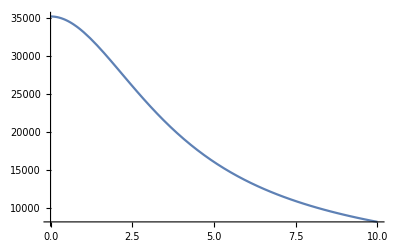

```mathematica
Plot[VE/.{α->alphaPt,A->APt,ϵ->1,R->r},{r,0,10}]
```

```mathematica
(*O-O interaction*)
```

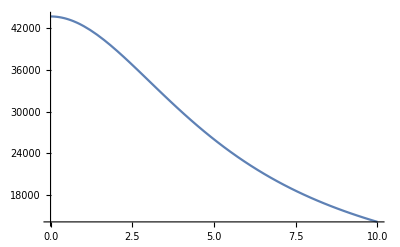

```mathematica
Plot[VE/.{α->alphaO,A->AO,ϵ->1,R->r},{r,0,10},PlotRange->All]
```

```mathematica
(*O-Pt interactions*)
```

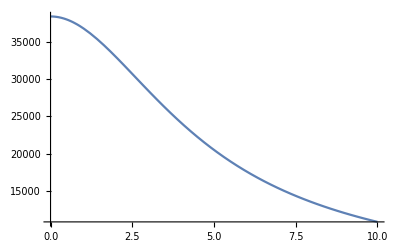

```mathematica
Plot[V/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO},{r,0,10}]
```

```mathematica
VE
```

(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(3 R α^6 ϵ)

```mathematica
sf = VE - (VE/.R->Rc) - (D[VE,R]\. R->Rc)*(R-Rc)
```

```mathematica
sf
```

sf

```mathematica
vp = D[VE,R] /. R->Rc
```

(A^2 ⅇ^(-Rc α) π (-33 α+48 ⅇ^(Rc α) α-18 Rc α^2-3 Rc^2 α^3))/(3 Rc α^6 ϵ)-(A^2 ⅇ^(-Rc α) π (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(3 Rc^2 α^6 ϵ)-(A^2 ⅇ^(-Rc α) π (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(3 Rc α^5 ϵ)

```mathematica
sp = VE - (VE/. R->Rc)
```

(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(3 R α^6 ϵ)-(A^2 ⅇ^(-Rc α) π (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(3 Rc α^6 ϵ)

```mathematica
sf = sp - vp * (R-Rc)
```

-(R-Rc) (-(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-α^2 (6+R α)+(2+R α) β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R^2 β^3 (α^3-α β^2)^3 ϵ)+(8 A B ⅇ^(-R (α+β)) π (-α-β) (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-α^2 (6+R α)+(2+R α) β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R β^3 (α^3-α β^2)^3 ϵ)+(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (α+β) (α^2-β^2)^3+ⅇ^(R β) β^4 (-α^3+α β^2)+ⅇ^(R β) β^5 (-α^2 (6+R α)+(2+R α) β^2)-ⅇ^(R α) α^4 (α^2 β-β^3)-ⅇ^(R α) α^5 (α^2 (2+R β)-β^2 (6+R β))))/(R β^3 (α^3-α β^2)^3 ϵ))+(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(3 R α^6 ϵ)-(A^2 ⅇ^(-Rc α) π (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(3 Rc α^6 ϵ)

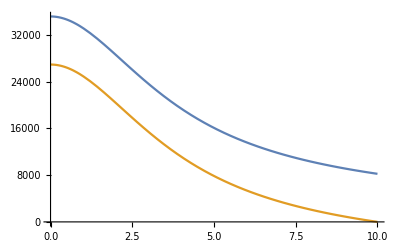

```mathematica
Plot[{VE/.{α->alphaPt,A->APt,ϵ->1,R->r,Rc->10}, sp/.{α->alphaPt,A->APt,ϵ->1,R->r,Rc->10}, sf/.{α->alphaPt,A->APt,ϵ->1,R->r,Rc->10}},{r,0,10}]
```